```mathematica
(* Homework 32*)
de=p'[t]==p[t]*(0.30-0.00004*p[t])
```

p'[t]==(0.3-0.00004 p[t]) p[t]

```mathematica
sol = DSolveValue[{de,p[0]==100},{p[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(8.24634×10^15 2.71828^(0.3 t))/(8.13639×10^13+1.09951×10^12 2.71828^(0.3 t))}

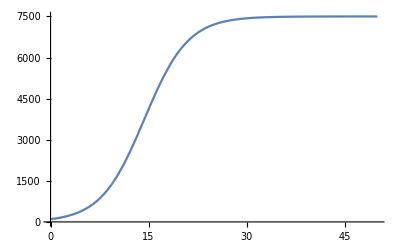

```mathematica
Plot[sol,{t,0,50}]
```

```mathematica
max=Limit[sol, t->100]
```

{7500.}

```mathematica
Solve[sol==.5*max,{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→14.3469}}

```mathematica
(* Homework 33*)
```

```mathematica
de1=200*q'[t]+(q[t]÷(3*10^(-6)))=1sin(377*t)
```

Set::write: Tag Plus in (1000000 q[t])/3+200 q'[t] is Protected.

377 sin t